## 4 loop running coupling

```mathematica
(* form hep-ph 9703284, vermaseren, larin, Ritbergen *)
ΛQCD=0.2145; 
(* so that for nF=5 we get alpha_s(mz=91.188)=0.1185 (PDG value) 
note that pdg also quotes λqcd=0.214 for nf=5 everything seems consistent*)

(*QCD*)
Nc=3.;CA=Nc; nF=3;
CF=(Nc^2-1)/(2 Nc);
(*coeft of the renormalization group equations*)
β0[Nf_]=(-11Nc+2Nf)/12;
β1[Nf_]=(-68 Nc^2+20Nc Nf+12CF Nf)/(3 32);
β2[Nf_]=-(2857-5033/9 Nf+325/27 Nf^2)/128; (*for Nc=3 only*)
β3[Nf_]=-1/256((149753/6+3564 Zeta[3])-(1078361/162+6508/27 Zeta[3])Nf+(50065/162+6472/81 Zeta[3])Nf^2+1093/729 Nf^3);(*for Nc=3 only*)

γ0[Nf_]=3/4 CF;
γ1[Nf_]=1/16(202/3-20/9 Nf);(*for Nc=3 only*)
γ2[Nf_]=1/64(1249+(-2216/27-160/3 Zeta[3])Nf-140/81 Nf^2);(*for Nc=3 only*)
γ3[Nf_]=1/256(4603055/162+135680/27 Zeta[3]-8800Zeta[5]+(-91723/27-34192/9 Zeta[3]+880 Zeta[4]+18400/9 Zeta[5])Nf+(5242/243+800/9 Zeta[3]-160/3 Zeta[4])Nf^2+(-332/243+64/27 Zeta[3])Nf^3);

b0[Nf_]=-(8β0[Nf])/(2(4π)^2);
b1[Nf_]=-(32 β1[Nf])/(2(4π)^2);

(* Initial conditions of the RG equations, μ in units of Λ_MSbar *)

(*gf[μ_]=1/√(2 b0 Log[μ]+b1 Log[2 Log[μ]]/b0);*)
gf[t_]=1/(√(b0[Nf] t+b1[Nf] Log[t]/b0[Nf]));
asf[t_,Nf_]=-1/(β0[Nf] t)-(β1[Nf] Log[t])/(β0[Nf]^3 t^2)-(β1[Nf]^2(Log[t]^2-Log[t]-1)+β2[Nf] β0[Nf])/(β0[Nf]^5 t^3)+1/(β0[Nf]^7 t^4)( β1[Nf]^3(-Log[t]^3+5/2 Log[t]^2+2Log[t]-1/2)-3 β1[Nf] β2[Nf] β0[Nf] Log[t]+1/2 β3[Nf] β0[Nf]^2);
μ0=2;
t0=Log[μ0^2];
tf=10000 t0;
(*solution of the RG equation to 3 loop*)
mcharm=1.275;(*m(m) in msbar*)
mbottom=4.18;
nf[t_]=If[t<Log[mcharm^2/ΛQCD^2],3,If[t<Log[mbottom^2/ΛQCD^2],4,5]];
sg4=Quiet[NDSolve[{D[as[t],t]==+β0[nf[t]] as[t]^2+β1[nf[t]] as[t]^3+ β2[nf[t]] as[t]^4+ β3[nf[t]] as[t]^5,as[tf]==asf[tf,nf[tf]]},as,{t,t0,tf},AccuracyGoal->14,WorkingPrecision->32,MaxSteps->10000000]];

a4t[t_]= Part[Evaluate[as[t]/.sg4],1];
g4[μ_]=2 π √Part[Evaluate[as[Log[μ^2/ΛQCD^2]]/.sg4],1];
```

## Cornell Potential Spectral Function

```mathematica
R=20000;
Mc=1.4690612135716832;
Mb=4.882;
kfinal={0.4709613222916442,-0.2550225519531524};
kfinalu={0.8020780608066254,-0.360468820434673};
kfinall={0.13984458377666326,-0.14957628347163182};
αcont={0.5137193759431391,0.0024666827878353577}; 
σcont={0.16955497884544793,0.0008581023195660334};
ccont={-0.15956635071361625,0.0024752900407607015};
```

```mathematica
ReVm0[r_,α_,σ_,c_]:=-α/r+σ r+c
```

```mathematica
Vsb[r_,α_,σ_,c_]:=HeavisideTheta[1.25/0.197-r](c-α/r+σ r)+HeavisideTheta[r-1.25/0.197](c-α/(1.25/0.197)+σ 1.25/0.197);
```

```mathematica
δ=1/100; 
dω=0.0002;ωmin= -1;ωmax=2;
ρtable=Table[{0,0},{x, ωmin, ωmax,dω Mc}];
SetSharedVariable[ρtable];
l=0;

ParallelDo[ω=ωmin+(it-1) dω Mc;inf=40+500*it*dω;
(*s0=NDSolve[{(ω-(l(l+1))/(M r^2)-Re[V[r]]+ⅈ Abs[Im[V[r]]])gr[r]+1/M gr''[r]==0, 
gr'[δ]==2 δ(α M)^2-3/4 δ^2(M α)^3,
 gr[δ]== δ^2(α M)^2-1/4 δ^3(M α)^3},gr,{r,δ,inf},PrecisionGoal->10,MaxSteps->1000000];
gr1[r_]=(gr[r]/.s0)_⟦1⟧;*)
s01=NDSolve[{(ω-(l(l+1))/(Mc r^2)-Re[Vsb[r,αcont[[1]],σcont[[1]],ccont[[1]]]]+ⅈ Abs[δ/10])gr[r]+1/Mc gr''[r]==0, 
gr'[δ]==(αcont[[1]] Mc)-δ(Mc αcont[[1]])^2,
 gr[δ]==δ(αcont[[1]] Mc)- 1/2 δ^2(αcont[[1]] Mc)^2},gr,{r,δ,inf},PrecisionGoal->10,AccuracyGoal->10,MaxSteps->1000000,Method->{"StiffnessSwitching","NonstiffTest"->False}];
gr0[r_]=(gr[r]/.s01)_⟦1⟧;
s1=NDSolve[{rho'[x]==-(6 Nc Mc^2 αcont[[1]])/(4π)Im[1/(gr0[x])^2(*+36/(gr1[x])^2*)],rho[δ]==0},rho,{x,δ,inf},PrecisionGoal->10,AccuracyGoal->10,MaxSteps->1000000];rhow[r_]=(rho[r]/.s1)_⟦1⟧;
ρtable[[it]]={ω+2Mc,rhow[inf]},{it,1,Length[ρtable]}];

ccsT=Table[{ρtable[[i]][[1]],(-ρtable[[i]][[2]])/(ρtable[[i]][[1]])^2},{i,1,Length[ρtable]}];
```

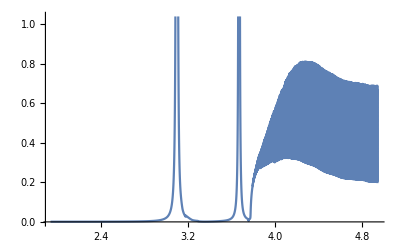

```mathematica
ListPlot[ccsT,Joined->True]
```